```mathematica
ImageListAdd[imgs_]:=Module[{r},
r=First@imgs;
Table[r=ImageAdd[r,i],{i,imgs[[2;;]]}];
r
]
ImageListMultiply[imgs_]:=Module[{r},
r=First@imgs;
Table[r=ImageMultiply[r,i],{i,imgs[[2;;]]}];
r
]
ImageListSubtract[img_,imgs_]:=Module[{r},
r=img;
Table[r=ImageSubtract[r,i],{i,imgs}];
r
]
```

1 | "CT-Knee_naive_optimized_green_1000"
2 | "CT-Knee_naive"
3 | "CT-Knee_strong_green"
4 | "CT-Knee_strong_red"
5 | "CT-Knee_weak_green_optimized_green_1000"
6 | "CT-Knee_weak_green"
7 | "CT-Knee_weak_red_optimized_red_1000"
8 | "CT-Knee_weak_red"
9 | "engine_medium_green"
10 | "engine_naive_optimized_green_1000"
11 | "engine_naive"
12 | "engine_strong_green"
13 | "engine_weak_green"
14 | "engine_weak_red_optimized_red_1000"
15 | "engine_weak_red"
16 | "foot_green_medium_optimized_green_1000"
17 | "foot_green_medium"
18 | "foot_green_strong"
19 | "foot_green_weak"
20 | "foot_naive_optimized_green_1000"
21 | "foot_naive"
22 | "horse_embryo_45_days_naive2_optimized_blue_1000"
23 | "horse_embryo_45_days_naive2"
24 | "horse_embryo_45_days_naive_optimized_blue_1000"
25 | "horse_embryo_45_days_naive"
26 | "MRbrain_naive_optimized_green_1000"
27 | "MRbrain_naive"
28 | "MRbrain_strong_green"
29 | "MRbrain_weak_green"
30 | "nucleon_naive_optimized_green_1000"
31 | "nucleon_naive_optimized_red_1000"
32 | "nucleon_naive"
33 | "nucleon_strong_red"
34 | "nucleon_weak_red"
35 | "tooth_naive_optimized_yellow_1000"
36 | "tooth_naive"
37 | "tooth_strong_yellow"
38 | "tooth_weak_yellow_optimized_yellow_1000"
39 | "tooth_weak_yellow"
40 | "vismale_naive_optimized_green_1000"
41 | "vismale_naive_optimized_red_1000"
42 | "vismale_naive"
43 | "vismale_strong_green"
44 | "vismale_strong_red"
45 | "vismale_weak_red"
46 | "vismale_week_green"

```mathematica
pnglist=Import[NotebookDirectory[]<>"~salience\\"<>"pnglist.xml"];
index=36;
a=First@pnglist[[index]];
b=Last@pnglist[[index]];
xmlname=StringReplace[Last@StringSplit[a,"\\"],".png"->".xml"]
dataname=StringReplace[xmlname,".xml"->""]
mixed=Import[a];
imglist=Import/@b;
{mixed,imglist}
```

tooth_naive.xml

tooth_naive

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
xml=Import[NotebookDirectory[]<>"~images\\"<>xmlname];
{tfifile,volumefile,legends,face,imagefilenames,featurefilename,resultxml,imagefile,dataname,plotpath,imagepath}=xml;
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
alpha=(#/255.&)/@a;
index=Flatten@Position[alpha,_?(#>0&)];
chartcolors=rgbcolors[[#]]&/@index;
```

30914.

{13969.6,2945.43,3597.16}

20512.2

{0.681038,0.143594,0.175367}

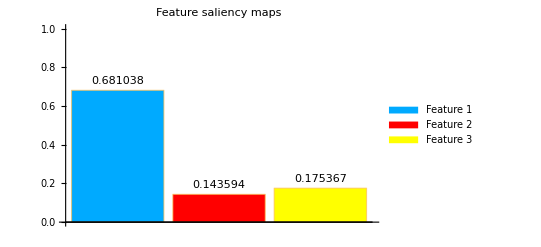

```mathematica
(*dist=ParallelMap[ColorDistance[#,mixed,DistanceFunction->"CIE2000"]&,imglist];*)
dist=ParallelMap[ColorDistance[#,mixed]&,imglist];
n=Length[imglist];
sets=Reverse@Subsets[Range[n],{n-1}];
subsets=Table[ImageListMultiply[dist[[#]]&/@s],{s,sets}];
denominator=ImageListAdd[subsets];
weights=ParallelMap[ImageApply[If[#2≠0,#1/#2,0]&,{#,denominator}]&,subsets];
saliency=ImageSaliencyFilter[mixed]
overlap=ParallelMap[ImageMultiply[saliency,#]&,weights]
ImageMeasurements[saliency,"TotalIntensity"]
features=ImageMeasurements[#,"TotalIntensity"]&/@overlap
Total[features]
ratio=features/Total[features]
legends={"Feature 1","Feature 2","Feature 3","Feature 4"};
BarChart[ratio,PlotLabel->"Feature saliency maps",ChartLegends->legends,ChartLabels->Placed[ToString/@ratio,Above],ChartStyle->chartcolors,PlotRange->{Automatic,{0,1}}]
```

```mathematica
(* use Gaussian kernel to smooth the overlap feature saliency maps *)
size=First@ImageDimensions[mixed]/8;
left=ImageListSubtract[saliency,overlap]
gaussian=ParallelMap[GaussianFilter[#,size]&,overlap];
ImageAdjust/@gaussian
sumOfGaussian=ImageListAdd[gaussian];
ratio=Table[ImageApply[If[#2≠0,Clip[#1/#2],0]&,{i,sumOfGaussian}],{i,gaussian}];
leftGaussian=ParallelMap[ImageMultiply[left,#]&,ratio]
weightedSaliency=Table[ImageAdd[overlap[[i]],leftGaussian[[i]]],{i,Length[overlap]}]
ImageMeasurements[saliency,"TotalIntensity"]
features2=ImageMeasurements[#,"TotalIntensity"]&/@weightedSaliency
Total[features2]
metric=features2/Total[features2]
```

30914.

{22424.6,3634.3,4339.81}

30398.7

{0.737683,0.119554,0.142763}

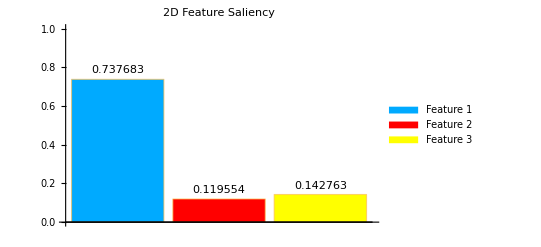

```mathematica
legends={"Feature 1","Feature 2","Feature 3","Feature 4"};
chart=BarChart[metric,PlotLabel->"2D Feature Saliency",ChartLegends->legends,ChartLabels->Placed[ToString/@metric,Above],ChartStyle->chartcolors,PlotRange->{Automatic,{0,1}}]
```

```mathematica
saliencemapoverlapstr=MapIndexed["_saliencemap_"<>ToString@First[#2]<>"_overlap"&,imglist];
saliencemapstr=MapIndexed["_saliencemap_"<>ToString@First[#2]&,imglist];
gaussianstr=MapIndexed["_gaussian_"<>ToString@First[#2]&,imglist];
leftgaussianstr=MapIndexed["_leftgaussian_"<>ToString@First[#2]&,imglist];
```

```mathematica
images=ImageMultiply[#,8]&/@Flatten@{saliency,left,overlap,weightedSaliency,gaussian,leftGaussian}
parts=Flatten@{"_saliencemap","_saliencemap_left",saliencemapoverlapstr,saliencemapstr,gaussianstr,leftgaussianstr};
filenames=(NotebookDirectory[]<>"~salience\\"<>dataname<>#<>".png")&/@parts;
Table[Export[filenames[[i]],images[[i]]],{i,Length[images]}];
Export[NotebookDirectory[]<>"~salience\\"<>dataname<>"_2DFS.png",chart];
```

```mathematica
dist=ParallelMap[ColorDistance[#,mixed,DistanceFunction->"CIE2000"]&,imglist]//AbsoluteTiming
dist=ParallelMap[ColorDistance[#,mixed]&,imglist]//AbsoluteTiming
```